```mathematica
sol =DSolve[{x''[t]+3x'[t] + 2x[t] ==  DiracDelta[t-5]-HeavisideTheta[t-10], x[0]==0, x'[0]==1/2}, x[t], t]
```

{{x[t]→-1/2 ⅇ^(-2 t) (1+ⅇ^20-ⅇ^t+ⅇ^(2 t)-2 ⅇ^(10+t)+2 ⅇ^10 HeavisideTheta[-5+t]-2 ⅇ^(5+t) HeavisideTheta[-5+t])+HeavisideTheta[10-t] (1/2 ⅇ^(-2 t) (1+ⅇ^20-ⅇ^t+ⅇ^(2 t)-2 ⅇ^(10+t)+2 ⅇ^10 HeavisideTheta[-5+t]-2 ⅇ^(5+t) HeavisideTheta[-5+t])+1/2 ⅇ^(-2 t) (-1+ⅇ^t-2 ⅇ^10 HeavisideTheta[-5+t]+2 ⅇ^(5+t) HeavisideTheta[-5+t]))}}

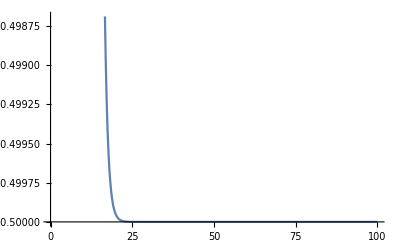

```mathematica
a = Plot[Evaluate[x[t]/.sol],{t,0,100}]
```

```mathematica
b = Plot[Evaluate[HeavisideTheta[t-5]*(Exp[-t+5]-Exp[-2t+10]) + (0.5*(Exp[-t]-Exp[-2t])) - HeavisideTheta[t-10](-Exp[-t+10]+0.5*Exp[-2*t+20]+0.5)], {t,0,100}]
```

-Graphics-

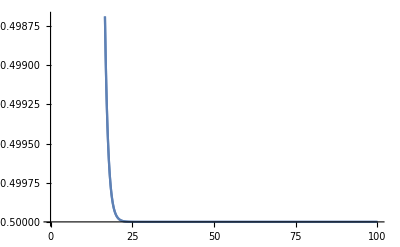

```mathematica
Show[a,b]
```

```mathematica
Simplify[sol]
```

{{x[t]→1/2 ⅇ^(-2 t) (-1-ⅇ^20+ⅇ^t-ⅇ^(2 t)+2 ⅇ^(10+t)+(ⅇ^10-ⅇ^t)^2 HeavisideTheta[10-t]+2 ⅇ^5 (-ⅇ^5+ⅇ^t) HeavisideTheta[-5+t])}}

```mathematica
Expand[%]
```

{{x[t]→-1/2-1/2 ⅇ^(20-2 t)+ⅇ^(10-t)-ⅇ^(-2 t)/2+ⅇ^-t/2+1/2 HeavisideTheta[10-t]+1/2 ⅇ^(20-2 t) HeavisideTheta[10-t]-ⅇ^(10-t) HeavisideTheta[10-t]-ⅇ^(10-2 t) HeavisideTheta[-5+t]+ⅇ^(5-t) HeavisideTheta[-5+t]}}

```mathematica
LaplaceTransform[DiracDelta[t-2*Pi]Exp[t], t, s]
```

ⅇ^(-2 π (-1+s))

```mathematica
DSolve[{x''[t]+x[t]==Cos[t]DiracDelta[t-2*Pi], x[0]==0, x'[0]==1}, x[t],t]
```

{{x[t]→Sin[t]+HeavisideTheta[-2 π+t] Sin[t]}}

```mathematica
sol1 = DSolve[{x''[t]+2x'[t]+2x[t] == Cos[t]-DiracDelta[t-(Pi/2)], x'[0]==x[0]==0}, x[t],t]
```

{{x[t]→1/10 ⅇ^-t (-2 Cos[t]+2 ⅇ^t Cos[t] Cos[2 t]+10 ⅇ^(π/2) Cos[t] HeavisideTheta[-π+2 t]-6 Sin[t]+5 ⅇ^t Sin[t]+ⅇ^t Cos[2 t] Sin[t]-ⅇ^t Cos[t] Sin[2 t]+2 ⅇ^t Sin[t] Sin[2 t])}}

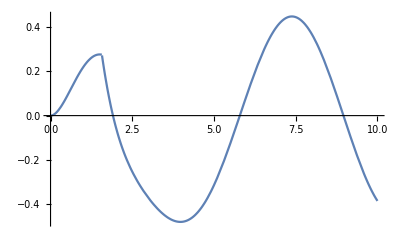

```mathematica
c =Plot[Evaluate[x[t]/.sol1], {t,0,10}]
```

-Graphics-

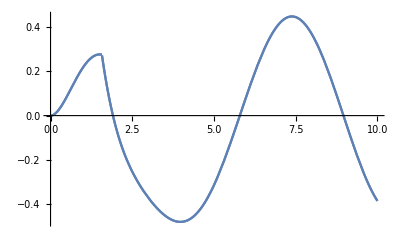

```mathematica
d= Plot[Evaluate[-0.2*Exp[-t]*Cos[t]-0.6*Exp[-t]*Sin[t]+0.2*Cos[t]+0.4*Sin[t] - Exp[-t+(Pi/2)]*HeavisideTheta[t-(Pi/2)]*Sin[t-(Pi/2)]], {t,0,10}]

Show[c,d]
```